```mathematica
FullSimplify[Solve[p(-Log[2,p]^λ)Log[-Log[2,p]]-(1-p)(-Log[2,1-p]^(1-λ))Log[-Log[2,1-p]]==0,λ]]
```

Solve::nsmet: 无法利用 Solve 现有的方法求解该系统.

$Aborted

```mathematica
{{λ->(-Log[p]+Log[-(-1+p) log[-log[2,1-p]]]-Log[log[-log[2,p]]]+Log[log[2,1-p]])/(Log[log[2,1-p]]+Log[log[2,p]])}}/.{p-> 0.2}
```

{{λ→(1.60944-Log[log[-log[2,0.2]]]+Log[0.8 log[-log[2,0.8]]]+Log[log[2,0.8]])/(Log[log[2,0.2]]+Log[log[2,0.8]])}}

```mathematica
H=-p(Log[1+λ]  Log[2,p])-(1-p)(Log[(1+1-λ)] Log[2,1-p])/.{p->0.319}
```

0.37746 Log[2-λ]+0.525831 Log[1+λ]

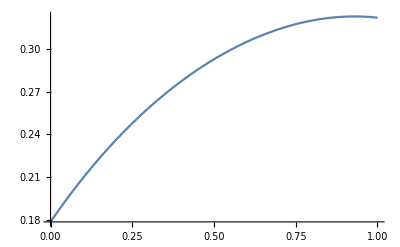

```mathematica
Plot[0.2575424759098898 Log[2-λ]+0.4643856189774725 Log[1+λ],{λ,0,1}]
```

```mathematica
DHλ=D[H,λ]
```

-0.37746/(2-λ)+0.525831/(1+λ)

Solve::nsmet: 无法利用 Solve 现有的方法求解该系统.

```mathematica
Solve[DHλ==0,λ,Method->Reduce]
```

Solve::ratnz: Solve 无法求解具有不精确系数的系统. 答案是通过求解相应的精确系统并且将结果数值化处理得到的.

{{λ→0.746383}}

```mathematica
Reduce[D[(Log[1-p]-p Log[1-p]-2 p Log[p])/(-Log[1-p]+p Log[1-p]-p Log[p]),p]<0,p]
```

0<p<1

```mathematica
H=-p λ Log[2,p]-(1-p)(1-λ)Log[2,1-p]
```

-((1-p) (1-λ) Log[1-p])/Log[2]-(p λ Log[p])/Log[2]

```mathematica
DHλ=D[H,λ]
```

((1-p) Log[1-p])/Log[2]-(p Log[p])/Log[2]

```mathematica
NumberForm[DHλ/.{p->0.2},3]
```

0.207

```mathematica
-p(Log[1+λ]  Log[2,p])-(1-p)(Log[(1+1-λ)] Log[2,1-p])/.{p->0.113}
```

0.153446 Log[2-λ]+0.355453 Log[1+λ]

```mathematica
FindRoot[0.15344566945022753 Log[2-λ]+0.3554534014138996 Log[1+λ]==0.21,{λ,1}]
```

{λ→0.527818}

```mathematica
-p(Log[1+λ]  Log[2,p])-(1-p)(Log[(1+1-λ)] Log[2,1-p])/.{p->0.319}
```

0.37746 Log[2-λ]+0.525831 Log[1+λ]

```mathematica
FindRoot[0.3774601150186608 Log[2-λ]+0.5258305630162124 Log[1+λ]==0.59,{λ,1}]
```

FindRoot::nlnum: 在 {λ} = {-1.} 处，函数值 {Indeterminate} 不是由数字组成的维度为 {1} 的列表.

{λ→0.746385}

```mathematica
-p(Log[1+λ]  Log[2,p])-(1-p)(Log[(1+1-λ)] Log[2,1-p])/.{p->0.146}
```

0.194449 Log[2-λ]+0.40529 Log[1+λ]

```mathematica
FindRoot[0.19444898938552357 Log[2-λ]+0.4052901199641821 Log[1+λ]==0.32,{λ,1}]
```

FindRoot::nlnum: 在 {λ} = {-1.} 处，函数值 {Indeterminate} 不是由数字组成的维度为 {1} 的列表.

{λ→1.0298}